```mathematica
comps = {"ax", "ay", "aeta"};
lattsize = "8x8";
(*Uncomment the next line to use a 64x64 lattice files*)
lattsize = "64x64";
```

```mathematica
For [icomp=1,icomp<=Length[comps],icomp++,
folder = "glasma_" <> lattsize <> "_latt_" <> comps[[icomp]] <> "_comp/";
folderpath= NotebookDirectory[] <> folder;

files=FileNames["*.txt",folderpath];
ntau = Length[files];

sortedfiles = SortBy[files,ToExpression@FileBaseName[#]&];
currentfile = sortedfiles[[1]];
currentdata = Import[currentfile, "Table"];
n = Sqrt[Length[currentdata]];
nadj = Length[currentdata[[1,All]]];

If[icomp==1,
(*Table[Ax[t,i,j,k],{t,ntau},{i,n},{j,n},{k,nadj}]*)
Ax= ConstantArray[Null, {ntau, n,n, nadj}],Indeterminate];
If[icomp==2, 
(*Table[Ay[t,i,j,k],{t,ntau},{i,n},{j,n},{k,nadj}]*)
Ay= ConstantArray[Null, {ntau, n,n, nadj}], Indeterminate];
If[icomp==3,
(*Table[Aeta[t,i,j,k],{t,ntau},{i,n},{j,n},{k,nadj}]*)
Aeta= ConstantArray[Null, {ntau, n,n, nadj}], Indeterminate];

For[itau=1,itau<=ntau,itau++,
currentfile = sortedfiles[[itau]];
data = Import[currentfile, "Table"];
For[i=1,i<=n,i++,
For[j=1,j<=n,j++,
For[k=1, k<=nadj,k++,
index = n*(i-1)+j;
(*If[icomp==1,Ax[itau,i,j,k]=data[[index,k]],Indeterminate];
If[icomp==2,Ay[itau,i,j,k]=data[[index,k]], Indeterminate];
If[icomp==3,Aeta[itau,i,j,k]=data[[index,k]], Indeterminate];*)
If[icomp==1,Ax[[itau,i,j,k]]=data[[index,k]],Indeterminate];
If[icomp==2,Ay[[itau,i,j,k]]=data[[index,k]], Indeterminate];
If[icomp==3,Aeta[[itau,i,j,k]]=data[[index,k]], Indeterminate];
]]]];
]
```

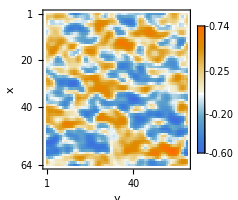
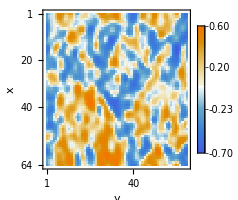
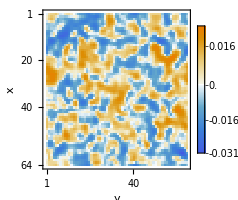

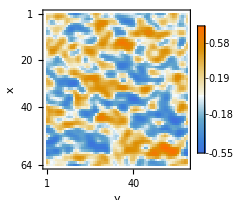
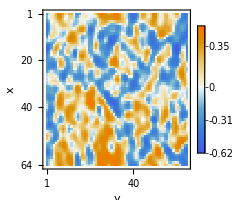
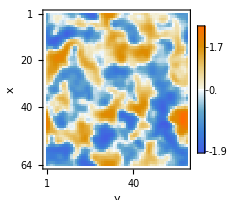

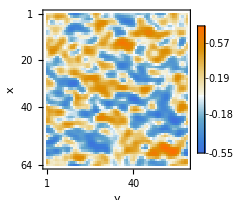
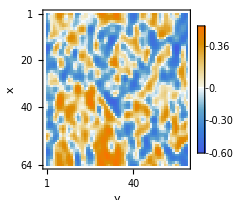

```mathematica
ic = 1;
label={"A_x","A_y","A_η"};
Do[
Amus = {Ax[[itau, All, All, ic]], Ay[[itau, All, All, ic]], Aeta[[itau, All, All, ic]]};
figs=Table[
figtitle=label[[iA]] <>"(τ="<>ToString[itau]<>")";
Amu=Amus[[iA]];
fig=MatrixPlot[
Amu,
PlotRange->All,
ImageSize->200,
PlotLegends->Automatic,
FrameLabel->{{"y",figtitle},{"x",None}}
],
{iA,1,3}
];
Row[figs]//Print
,{itau,1,ntau+1,(ntau-Mod[ntau, 3])/3}]
```